```mathematica
({{2.1724007034307707 10^-06, 7.627221665219164 10^-12}, {2.7557343862331254 10^-07, 2.447248050160144 10^-11}, {8.205618931236921 10^-08, 8.717873270425288 10^-11}, {3.470344185902262 10^-08, 2.6548595026072 10^-10}, {1.779467642810426 10^-08, 7.518191694262277 10^-10}})
```

{{2.1724×10^-6,7.62722×10^-12},{2.75573×10^-7,2.44725×10^-11},{8.20562×10^-8,8.71787×10^-11},{3.47034×10^-8,2.65486×10^-10},{1.77947×10^-8,7.51819×10^-10}}

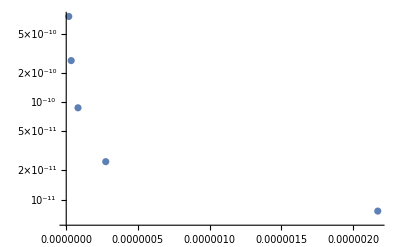

```mathematica
ListLogPlot[({{2.1724007034307707 10^-06, 7.627221665219164 10^-12}, {2.7557343862331254 10^-07, 2.447248050160144 10^-11}, {8.205618931236921 10^-08, 8.717873270425288 10^-11}, {3.470344185902262 10^-08, 2.6548595026072 10^-10}, {1.779467642810426 10^-08, 7.518191694262277 10^-10}})]
```

```mathematica
Fit[({{1/10, 7.627221665219164 10^-12}, {1/20, 2.447248050160144 10^-11}, {1/30, 8.717873270425288 10^-11}, {1/40, 2.6548595026072 10^-10}, {1/50, 7.518191694262277 10^-10}}), {1,x*x,x*x*x,x*x*x*x,x*x*x*x*x},x]
```

3.84996×10^-9-0.000021514 x^2+0.000954155 x^3-0.0147506 x^4+0.0732203 x^5

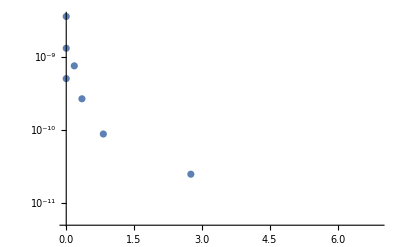

```mathematica
Show[ListLogPlot[({{2.1724007034307707 10^-06, 7.627221665219164 10^-12}, {2.7557343862331254 10^-07, 2.447248050160144 10^-11}, {8.205618931236921 10^-08, 8.717873270425288 10^-11}, {3.470344185902262 10^-08, 2.6548595026072 10^-10}, {1.779467642810426 10^-08, 7.518191694262277 10^-10}, {0, 5.022369353332074*^-10}, {0, 1.3124650421230262*^-9}, {0, 3.5832104696077976*^-9}})]]
```

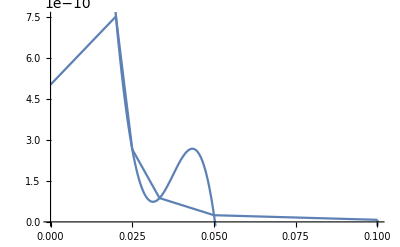

```mathematica
Show[ListPlot[({{1/10, 7.627221665219164 10^-12}, {1/20, 2.447248050160144 10^-11}, {1/30, 8.717873270425288 10^-11}, {1/40, 2.6548595026072 10^-10}, {1/50, 7.518191694262277 10^-10}, {0, 5.022369353332074*^-10}}),Joined->True],Plot[3.849961650525702*^-9-0.000021513983264548503 x^2+0.000954155357583962 x^3-0.014750605632454004 x^4+0.07322027038780633 x^5,{x,0,1/10}]]
```

```mathematica
Fit[({{10, 7.627221665219164 10^-12}, {20, 2.447248050160144 10^-11}, {30, 8.717873270425288 10^-11}, {40, 2.6548595026072 10^-10}, {50, 7.518191694262277 10^-10}}), {1,x*x,x*x*x,x*x*x*x,x*x*x*x*x},x]
```

1.08945×10^-11-1.54441×10^-13 x^2+1.62458×10^-14 x^3-4.72481×10^-16 x^4+6.55779×10^-18 x^5

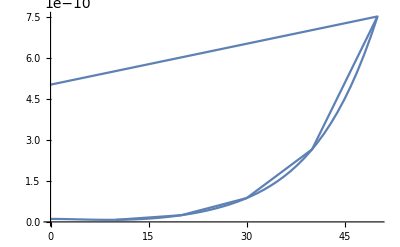

```mathematica
Show[ListPlot[({{10, 7.627221665219164 10^-12}, {20, 2.447248050160144 10^-11}, {30, 8.717873270425288 10^-11}, {40, 2.6548595026072 10^-10}, {50, 7.518191694262277 10^-10}, {0, 5.022369353332074*^-10}}),Joined->True],Plot[1.0894544916033504*^-11-1.5444075754222255*^-13 x^2+1.6245783574161538*^-14 x^3-4.724810267080642*^-16 x^4+6.557791963267067*^-18 x^5,{x,0,50}]]
```

PERFECT CONVERGENCE OF N → ∞ at gK = 0.5

Arrow

2.7127×10^-8-1.0486×10^-7 x

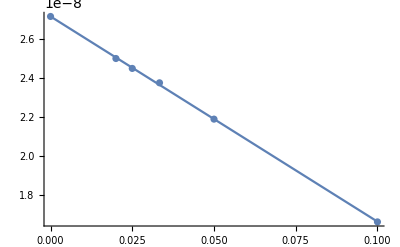

```mathematica
Fit[({{1/10, 1.6627452406022648 10^-08}, {1/20, 2.187969554094676 10^-08}, {1/30, 2.3735838401010163 10^-08}, {1/40, 2.4471009939116838 10^-08}, {1/50, 2.4978062835672475 10^-08}, {0, 2.7127005559869763 10^-08}}), {1,x},x]
Show[ListPlot[({{1/10, 1.6627452406022648 10^-08}, {1/20, 2.187969554094676 10^-08}, {1/30, 2.3735838401010163 10^-08}, {1/40, 2.4471009939116838 10^-08}, {1/50, 2.4978062835672475 10^-08}, {0, 2.7127005559869763 10^-08}}),Joined->False],Plot[2.7127005559869773*^-8-1.0485971683173706*^-7 x,{x,0,1/10}]]
```

PERFECT CONVERGENCE OF N → ∞ at gK = 0.6

3.95448×10^-7-1.1922×10^-6 x

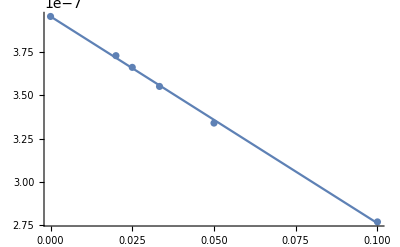

```mathematica
Fit[({{1/10, 2.7699946108616576 10^-07}, {1/20, 3.339749074065196 10^-07}, {1/30, 3.5510216633886407 10^-07}, {1/40, 3.660991149037772 10^-07}, {1/50, 3.7284619836748787 10^-07}, {0, 3.954481139219577 10^-07}}), {1,x},x]
Show[ListPlot[({{1/10, 2.7699946108616576 10^-07}, {1/20, 3.339749074065196 10^-07}, {1/30, 3.5510216633886407 10^-07}, {1/40, 3.660991149037772 10^-07}, {1/50, 3.7284619836748787 10^-07}, {0, 3.954481139219577 10^-07}}),Joined->False],Plot[3.9544811392195777*^-7-1.1921987803225125*^-6 x,{x,0,1/10}]]
```